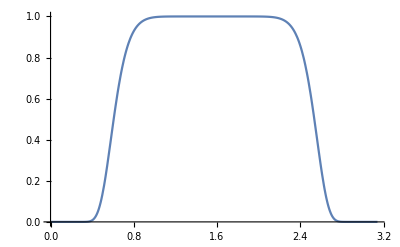

```mathematica
Plot[Exp[-(x-π/2)^10], {x,0, π}, PlotRange->All]
```

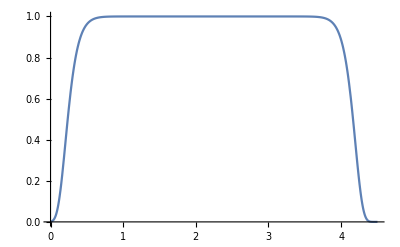

```mathematica
Plot[Exp[-((x-2.2)/2)^20], {x,0,4.5}, PlotRange->All]
```

```mathematica
swf=Table[Tanh[10 x]- HeavisideTheta[x-5] Tanh[10 x], {x, 0, 10,.1}];
```

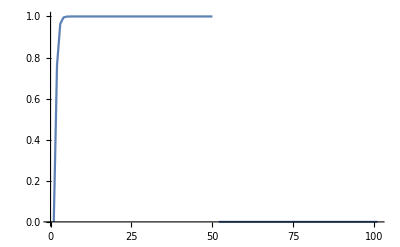

```mathematica
ListPlot[swf, Joined->True]
```

```mathematica
LaplaceTransform[Tanh[10 t]- HeavisideTheta[t-5] Tanh[10 t],t,s]
```

-ⅇ^(-5 s)/s+1/10 (-(-1)^(s/20) Beta[-ⅇ^100,-s/20,0]-π Csc[(π s)/20])+1/20 (-20/s-PolyGamma[0,s/40]+PolyGamma[0,(20+s)/40])

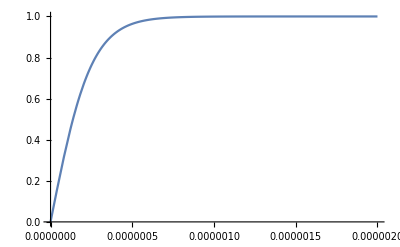

```mathematica
Plot[Tanh[4 10^6 x], {x, 0, 2 10^-6}, PlotRange->All]
```

```mathematica
Tanh[4 10^6 x]/.x-> .5 10^-6
```

0.964028

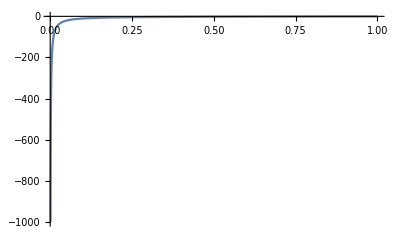

```mathematica
Plot[PolyGamma[0,x],{x,10^-3,1.0}, PlotRange->All]
```

```mathematica
FullSimplify[LaplaceTransform[Tanh[k δ t],t,s], Assumptions->{k>0, δ>0}]
```

(-2 k δ+s PolyGamma[0,1/4 (2+s/(k δ))]-s PolyGamma[0,s/(4 k δ)])/(2 k s δ)

```mathematica
f[s_]:=(5.*^-7 Gamma[0.+5.*^-7 s] Hypergeometric2F1[1.,0.+5.*^-7 s,1.+5.*^-7 s,-1])/Gamma[1.+5.*^-7 s]-(5.*^-7 Gamma[1+5.*^-7 s] Hypergeometric2F1[1.,1+5.*^-7 s,2+5.*^-7 s,-1])/Gamma[2+5.*^-7 s]
```

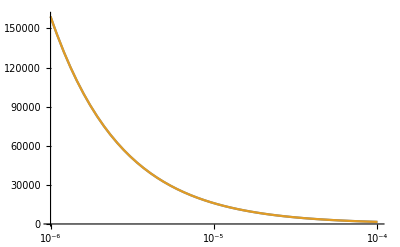

```mathematica
LogLinearPlot[{Abs[f[I 2π x]],Abs[1/(I 2π x)]}, {x, 10^-6, .00010}, PlotRange->All]
```